```mathematica
ClearAll["Global`*"]
```

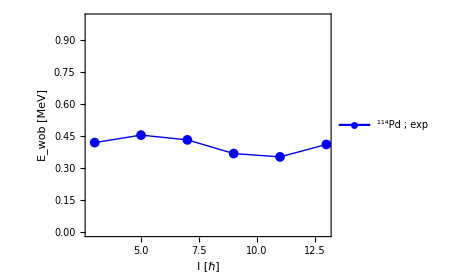

```mathematica
yrastEn=Sort[{5011.6,4147.3,3443.2,2859.7,2215.7,1500.51,852.37,332.61,0}];
wob1En=Sort[{4205.7,3503.9,2905.7,2290.0,1630.69,1011.65}];
yrastSpin=Table[i,{i,0,16,2}];
wob1Spin=Table[i,{i,3,13,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+1]]+yrast[[i+2]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","114"],"Pd ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/114Pd.pdf",fig];
Show[fig]
```